```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]
κσr = Last[Flatten[StringSplit[FileNames["KAPPA_SIGMA_R_*",NotebookDirectory[]],"_"]]];
```

/homes/ht/Desktop/collagen/collagen_results/kappa6

```mathematica
DataPlots=Table[{StringSplit[FileNames["Analysis*"][[i]],"_"][[2]],
path=FileNames["Analysis*"][[i]]<>"/";
{Import[path<>"new2_force.data","Table"]}},{i,1,Length[FileNames["Analysis*"]]}];
```

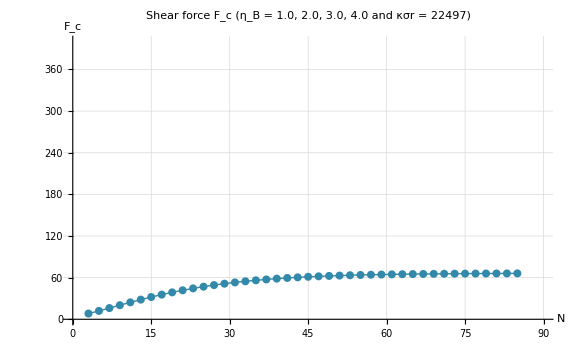

InterpolatingFunction[{{3.,85.}},<>]

```mathematica
fsTitle=24;
fsAxesLabel=18;
fs2=16;

ListLinePlot[
{
DataPlots[[1,2]][[1]]
},
PlotRange->{{0,90},{0,400}},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
AxesLabel->{
Style["N",FontSize->fsAxesLabel],
Style["F_c",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
Mesh->All,
PlotStyle->{RGBColor[50/255,137/255,170/255],PointSize[0.01]},
PlotLabel->Style["Shear force F_c (η_B = "<>ToString[DataPlots[[1,1]]]<>", " <>ToString[DataPlots[[2,1]]]<>", " <>ToString[DataPlots[[3,1]]]<>", " <>ToString[DataPlots[[4,1]]]<>" and κσr = "<>ToString[κσr]<>")",FontSize->fsTitle],
ImageSize->Large
]
InterF=Interpolation[DataPlots[[1,2]][[1]]]
func[x_]:=Round[If[x<80,InterF[x],InterF[85]],0.001]
```

N | P(N)
17 | 0.0273973
50 | 0.0273973
183 | 0.0273973
217 | 0.0547945
250 | 0.0410959
283 | 0.0547945
350 | 0.0273973
417 | 0.0821918
450 | 0.383562
483 | 0.0547945
517 | 0.0273973
550 | 0.0410959
583 | 0.0136986
617 | 0.0273973
650 | 0.0273973
683 | 0.0136986
717 | 0.0273973
750 | 0.0273973
883 | 0.0136986

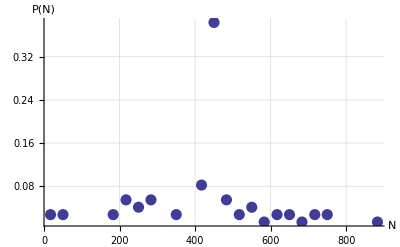

-Graphics-

```mathematica
TropocollagenLength=300;
TotalResiduesInTC=1000;
ResiduePerNanoMeter=TotalResiduesInTC/TropocollagenLength//N;

d={{5,2},{15,2},{55,2},{65,4},{75,3},{85,4},{105,2},{125,6},{135,28},{145,4},{155,2},{165,3},{175,1},{185,2},{195,2},{205,1},{215,2},{225,2},{265,1}};
totalCount=Total[Last[Transpose[d]]];

dw=Table[{Round[d[[idx,1]]*ResiduePerNanoMeter],(*d[[idx,2]],*)d[[idx,2]]/totalCount//N},{idx,1,Length[d]}];
Grid[Prepend[dw,{"N","P(N)"}]]

ListPlot[dw,PlotRange->All,AxesOrigin->{0,0},
GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],
PlotStyle->PointSize[0.02],
AxesLabel->{Style["N",FontSize->fsAxesLabel],Style["P(N)",FontSize->fsAxesLabel]},LabelStyle->{FontSize->fs2},BaseStyle->{FontFamily->"Helvetica"}]
```

{{35.54,0.0273973},{62.741,0.0273973},{66.127,0.945205}}

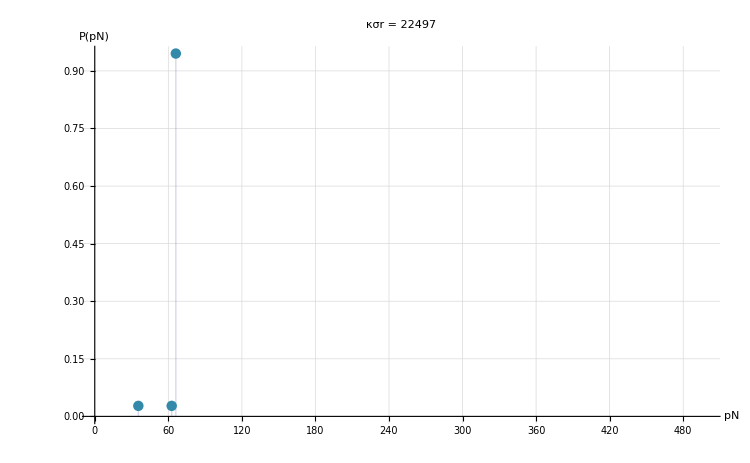

```mathematica
ForceDistributionData=Table[{func[dw[[idx,1]]],dw[[idx,2]]},{idx,1,Length[dw]}];
Forces=Union[Transpose[ForceDistributionData][[1]]];
ForceProbDistributionData=Table[
{
Forces[[i]],
ListToSum=First[Transpose[Position[ForceDistributionData,Forces[[i]]]]];Sum[ForceDistributionData[[ListToSum[[idx]],2]],{idx,1,Length[ListToSum]}]
}
,{i,1,Length[Forces]}
]
ListPlot[{ForceProbDistributionData},PlotStyle->{RGBColor[50/255,137/255,170/255],PointSize[0.01]},PlotRange->{{0,500},Automatic},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],Filling->Axis,AxesLabel->{Style["pN",FontSize->fsAxesLabel],Style["P(pN)",FontSize->fsAxesLabel]},LabelStyle->{FontSize->fs2},Mesh->All,BaseStyle->{FontFamily->"Helvetica"},
PlotLabel->Style["κσr = "<>ToString[κσr],FontSize->fsTitle],ImageSize->750]
```